```mathematica
ClearAll["Global`*"]
```

```mathematica
nmsq[v_]:=v.v
nm[v_]:=If[nmsq[v]=0,1,Sqrt[nmsq[v]]]
epsilon=.00001
```

0.00001

```mathematica
Table[Cylinder[{{0,0,-1},{0,0,-1+i/55}},1],{i,-55,55,2}];
```

```mathematica
picture[X_]:=Graphics3D[{PointSize[Large],Point@X,Opacity[.5], Sphere[{0,0,0}]}, Boxed->False,ImageSize->Medium];
picture2[X_]:=Graphics3D[{PointSize[Large],Point@X,Opacity[.5],White, Cylinder[{{0,0,-1},{0,0,1}},1],

Red,Table[Cylinder[{{0,0,-1+i/55},{0,0,-1+(i+2)/55}},1],{i,0,110,4}]




}, Boxed->False,ImageSize->Medium,ViewPoint->{0,Infinity,0}];


picture3[X_,n_,o1_,o2_]:=Graphics3D[{

Red,Opacity[o2],Table[Cylinder[{{0,0,-1+i/Fibonacci[n]},{0,0,-1+(i+2)/Fibonacci[n]}},1-epsilon],{i,0,2*Fibonacci[n],4}]
,Opacity[o1],White, Cylinder[{{0,0,-1},{0,0,1}},1-epsilon],
Opacity[1],Black,PointSize[Large],Point@X

}, Boxed->False,ImageSize->Medium,ViewPoint->{0,Infinity,0},ImageSize->Large]
```

```mathematica
(*Code for generating spiral points of various types, adapted from code of Brauchart et. al.*)

phi[x_,y_]:={2 √(y-y^2)Cos[2π x],2 √(y-y^2)Sin[2π x],1-2y};

psi[{x_,y_,z_}]:={x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2],z}

phi::usage="Lambert Projection";

FLPS[n_]:=Module[{Fn,r},Fn=Fibonacci[n];r=Fibonacci[n-1]/Fn;Table[{k/Fn,FractionalPart[k r]},{k,0,Fn-1}]];
FLPS::usage = "generates the nth fibonacci lattice in the square";

sphFLPS[n_]:=phi[#[[1]],#[[2]]]&/@FLPS[n];
sphFLPS::usage = "projects fibonacci lattice to the sphere";
```

```mathematica
Solve[phi[x,y]=={0,1,0},{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/4,y→1/2}}

```mathematica
CFLPS[n_,irr_]:=Module[{r},
r=irr;
Table[{k/n,FractionalPart[k r]},{k,0,n-1}]];
(*CFLPS[n_,irr_]:=Module[{r},

r=FromContinuedFraction[ContinuedFraction[irr,n]];
Table[{k/n,FractionalPart[k r]},{k,0,n-1}]];*)
CFLPS::usage = "generates the n points on lattice offset by irrational number in the square";

sphCFLPS[n_,irr_]:=phi[#[[1]],#[[2]]]&/@CFLPS[n,irr];

CFLPSd[n_,irr_]:=Module[{r,d},
r=FromContinuedFraction[ContinuedFraction[irr,n]];
d=Denominator[r];
Table[{k/d,FractionalPart[k r]},{k,0,d-1}]];
CFLPSd::usage = "generates the denominator of the depth n continued fraction number of points on lattice offset by irrational approximation in the square";

sphCFLPSd[n_,irr_]:=phi[#[[1]],#[[2]]]&/@CFLPSd[n,irr];

FLPS[10]//Length
```

55

```mathematica
ContinuedFraction[GoldenRatio,10]
ContinuedFraction[1/GoldenRatio,10]
```

{1,1,1,1,1,1,1,1,1,1}

{0,1,1,1,1,1,1,1,1,1}

```mathematica
Table[{i/55,j/55},{i,0,10},{j,0,10}]//Flatten[#,1]&
```

{{0,0},{0,1/55},{0,2/55},{0,3/55},{0,4/55},{0,1/11},{0,6/55},{0,7/55},{0,8/55},{0,9/55},{0,2/11},{1/55,0},{1/55,1/55},{1/55,2/55},{1/55,3/55},{1/55,4/55},{1/55,1/11},{1/55,6/55},{1/55,7/55},{1/55,8/55},{1/55,9/55},{1/55,2/11},{2/55,0},{2/55,1/55},{2/55,2/55},{2/55,3/55},{2/55,4/55},{2/55,1/11},{2/55,6/55},{2/55,7/55},{2/55,8/55},{2/55,9/55},{2/55,2/11},{3/55,0},{3/55,1/55},{3/55,2/55},{3/55,3/55},{3/55,4/55},{3/55,1/11},{3/55,6/55},{3/55,7/55},{3/55,8/55},{3/55,9/55},{3/55,2/11},{4/55,0},{4/55,1/55},{4/55,2/55},{4/55,3/55},{4/55,4/55},{4/55,1/11},{4/55,6/55},{4/55,7/55},{4/55,8/55},{4/55,9/55},{4/55,2/11},{1/11,0},{1/11,1/55},{1/11,2/55},{1/11,3/55},{1/11,4/55},{1/11,1/11},{1/11,6/55},{1/11,7/55},{1/11,8/55},{1/11,9/55},{1/11,2/11},{6/55,0},{6/55,1/55},{6/55,2/55},{6/55,3/55},{6/55,4/55},{6/55,1/11},{6/55,6/55},{6/55,7/55},{6/55,8/55},{6/55,9/55},{6/55,2/11},{7/55,0},{7/55,1/55},{7/55,2/55},{7/55,3/55},{7/55,4/55},{7/55,1/11},{7/55,6/55},{7/55,7/55},{7/55,8/55},{7/55,9/55},{7/55,2/11},{8/55,0},{8/55,1/55},{8/55,2/55},{8/55,3/55},{8/55,4/55},{8/55,1/11},{8/55,6/55},{8/55,7/55},{8/55,8/55},{8/55,9/55},{8/55,2/11},{9/55,0},{9/55,1/55},{9/55,2/55},{9/55,3/55},{9/55,4/55},{9/55,1/11},{9/55,6/55},{9/55,7/55},{9/55,8/55},{9/55,9/55},{9/55,2/11},{2/11,0},{2/11,1/55},{2/11,2/55},{2/11,3/55},{2/11,4/55},{2/11,1/11},{2/11,6/55},{2/11,7/55},{2/11,8/55},{2/11,9/55},{2/11,2/11}}

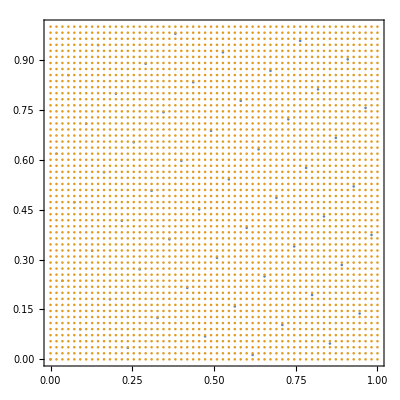

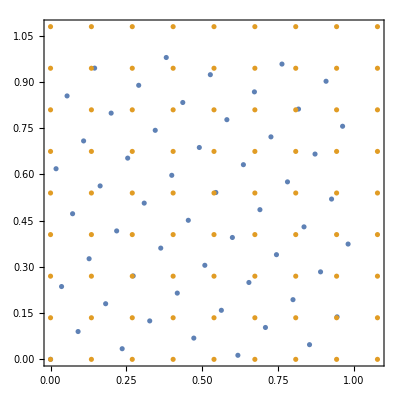

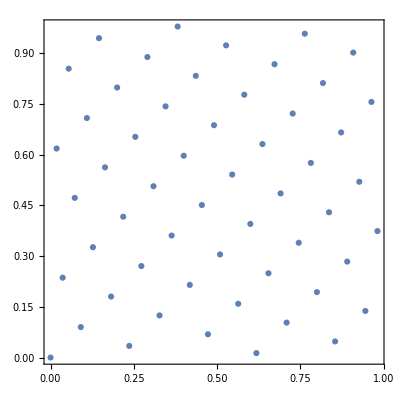

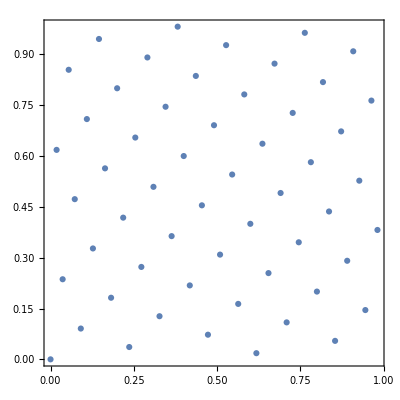

```mathematica
ListPlot[Union[{CFLPS[55,GoldenRatio],Table[{i/55,j/55},{i,0,55},{j,0,55}]//Flatten[#,1]&}],AspectRatio->Automatic,Frame->True]

ListPlot[Union[{CFLPS[55,GoldenRatio],Table[{i/Sqrt[55],j/Sqrt[55]},{i,0,8},{j,0,8}]//Flatten[#,1]&}],AspectRatio->Automatic,Frame->True]

ListPlot[CFLPS[55,GoldenRatio^-1],AspectRatio->Automatic,Frame->True]
ListPlot[FLPS[10],AspectRatio->Automatic,Frame->True]
```

-Graphics-

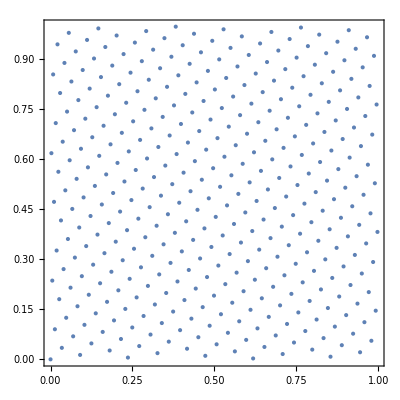

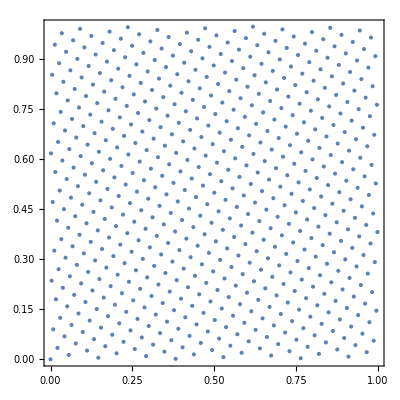

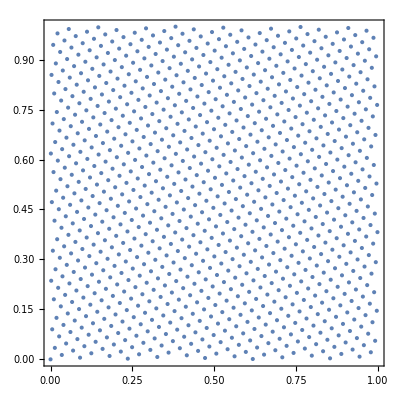

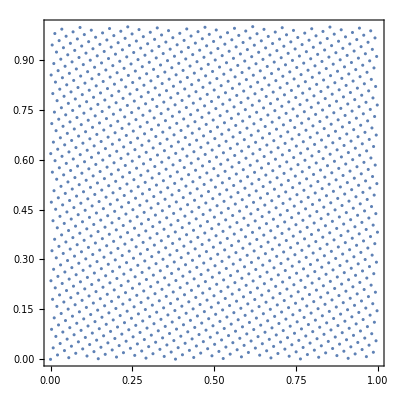

```mathematica
ListPlot[{CFLPS[1597,GoldenRatio],Table[{i/1597,j/1597},{i,0,1597},{j,0,1597}]//Flatten[#,1]&},AspectRatio->Automatic,Frame->True]
ListPlot[FLPS[14],AspectRatio->Automatic,Frame->True]
ListPlot[FLPS[15],AspectRatio->Automatic,Frame->True]
ListPlot[FLPS[16],AspectRatio->Automatic,Frame->True]
ListPlot[FLPS[17],AspectRatio->Automatic,Frame->True]
```

```mathematica
W=sphFLPS[17];
X=sphCFLPSd[17,GoldenRatio];
Y=sphCFLPS[1597,GoldenRatio];
X1=sphCFLPSd[17,1/GoldenRatio];
Y1=sphCFLPS[1597,1/GoldenRatio];
```

```mathematica
W==X
X==Y
Fibonacci[17]
{Length[X],picture[X//N]}
{Length[Y],picture[Y//N]}
{Length[X1],picture[X1//N]}
{Length[Y1],picture[Y1//N]}
X1==X
```

True

False

1597

{1597,-Graphics3D-}

{1597,-Graphics3D-}

{1597,-Graphics3D-}

«1 more identical outputs»

True

```mathematica
exportfibp[X_]:=Export[ToString[X]<>"fib.csv",sphFLPS[X]//N]
```

```mathematica
exportfibp[16]
```

16fib.csv

```mathematica
(*Random Points*)

unipoint[u_,t_]:={Sqrt[1-u^2]Cos[t],Sqrt[1-u^2]Sin[t],u}
SeedRandom[621859188853648];
randomSP[k_]:=Table[unipoint[RandomReal[{-1,1}], RandomReal[{0,2Pi}]],{i,k}]
```

```mathematica
picture[randomSP[1597]]
```

-Graphics3D-

```mathematica
(RotationMatrix[Pi/2,{0,1,0}].#&/@sphFLPS[10])//Solve[phi[x,y]==#,{x,y}]&/@#&;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

```mathematica
{x,y}/.#&/@{{{x->0,y->1/2}},{{x->ArcCos[-13/(√(169+2856 Sin[(2 π)/55]^2))]/(2 π),y->1/110 (55+2 √714 Cos[(2 π)/55])}},{{x->ArcCos[29/(√(841+2184 Sin[(4 π)/55]^2))]/(2 π),y->1/110 (55+2 √546 Cos[(4 π)/55])}},{{x->ArcCos[-39/(√(1521+1504 Sin[(6 π)/55]^2))]/(2 π),y->1/110 (55+4 √94 Cos[(6 π)/55])}},{{x->ArcCos[3/(√(9+3016 Sin[(8 π)/55]^2))]/(2 π),y->1/110 (55+2 √754 Cos[(8 π)/55])}},{{x->ArcCos[9/(√(81+40 Sin[(2 π)/11]^2))]/(2 π),y->1/22 (11+2 √10 Cos[(2 π)/11])}},{{x->ArcCos[-23/(√(529+2496 Sin[(12 π)/55]^2))]/(2 π),y->1/110 (55+8 √39 Cos[(12 π)/55])}},{{x->ArcCos[19/(√(361+2664 Cos[(27 π)/110]^2))]/(2 π),y->1/110 (55+6 √74 Sin[(27 π)/110])}},{{x->ArcCos[-49/(√(2401+624 Cos[(23 π)/110]^2))]/(2 π),y->1/110 (55+4 √39 Sin[(23 π)/110])}},{{x->ArcCos[-7/(√(49+2976 Cos[(19 π)/110]^2))]/(2 π),y->1/110 (55+4 √186 Sin[(19 π)/110])}},{{x->ArcCos[7/(√(49+72 Cos[(3 π)/22]^2))]/(2 π),y->1/22 (11+6 √2 Sin[(3 π)/22])}},{{x->ArcCos[-3 √(1/341 (19-2 √5))]/(2 π),y->1/10 (4+√5)}},{{x->ArcCos[9/(√(81+2944 Cos[(7 π)/110]^2))]/(2 π),y->1/110 (55+8 √46 Sin[(7 π)/110])}},{{x->ArcCos[51/(√(2601+424 Cos[(3 π)/110]^2))]/(2 π),y->1/110 (55+2 √106 Sin[(3 π)/110])}},{{x->ArcCos[-17/(√(289+2736 Cos[π/110]^2))]/(2 π),y->1/110 (55-12 √19 Sin[π/110])}},{{x->ArcCos[5/(√(25+96 Cos[π/22]^2))]/(2 π),y->1/22 (11-4 √6 Sin[π/22])}},{{x->ArcCos[-43/(√(1849+1176 Cos[(9 π)/110]^2))]/(2 π),y->1/110 (55-14 √6 Sin[(9 π)/110])}},{{x->ArcCos[-1/(√(1+3024 Cos[(13 π)/110]^2))]/(2 π),y->1/110 (55-12 √21 Sin[(13 π)/110])}},{{x->ArcCos[41/(√(1681+1344 Cos[(17 π)/110]^2))]/(2 π),y->1/110 (55-8 √21 Sin[(17 π)/110])}},{{x->ArcCos[-27/(√(729+2296 Cos[(21 π)/110]^2))]/(2 π),y->1/110 (55-2 √574 Sin[(21 π)/110])}},{{x->ArcCos[3/(√(9+112 Cos[(5 π)/22]^2))]/(2 π),y->1/22 (11-4 √7 Sin[(5 π)/22])}},{{x->ArcCos[-53/(√(2809+216 Sin[(13 π)/55]^2))]/(2 π),y->1/110 (55-6 √6 Cos[(13 π)/55])}},{{x->ArcCos[-√(1/211 (16+3 √5))]/(2 π),y->1/20 (10-√6-√30)}},{{x->ArcCos[31/(√(961+2064 Sin[(9 π)/55]^2))]/(2 π),y->1/110 (55-4 √129 Cos[(9 π)/55])}},{{x->ArcCos[-37/(√(1369+1656 Sin[(7 π)/55]^2))]/(2 π),y->1/110 (55-6 √46 Cos[(7 π)/55])}},{{x->ArcCos[1/(√(1+120 Sin[π/11]^2))]/(2 π),y->1/22 (11-2 √30 Cos[π/11])}},{{x->ArcCos[47/(√(2209+816 Sin[(3 π)/55]^2))]/(2 π),y->1/110 (55-4 √51 Cos[(3 π)/55])}},{{x->ArcCos[-21/(√(441+2584 Sin[π/55]^2))]/(2 π),y->1/110 (55-2 √646 Cos[π/55])}},{{x->-ArcCos[21/(√(441+2584 Sin[π/55]^2))]/(2 π),y->1/110 (55-2 √646 Cos[π/55])}},{{x->-ArcCos[-47/(√(2209+816 Sin[(3 π)/55]^2))]/(2 π),y->1/110 (55-4 √51 Cos[(3 π)/55])}},{{x->-ArcCos[-1/(√(1+120 Sin[π/11]^2))]/(2 π),y->1/22 (11-2 √30 Cos[π/11])}},{{x->-ArcCos[37/(√(1369+1656 Sin[(7 π)/55]^2))]/(2 π),y->1/110 (55-6 √46 Cos[(7 π)/55])}},{{x->-ArcCos[-31/(√(961+2064 Sin[(9 π)/55]^2))]/(2 π),y->1/110 (55-4 √129 Cos[(9 π)/55])}},{{x->-ArcCos[√(1/211 (16+3 √5))]/(2 π),y->1/20 (10-√6-√30)}},{{x->-ArcCos[53/(√(2809+216 Sin[(13 π)/55]^2))]/(2 π),y->1/110 (55-6 √6 Cos[(13 π)/55])}},{{x->-ArcCos[-3/(√(9+112 Cos[(5 π)/22]^2))]/(2 π),y->1/22 (11-4 √7 Sin[(5 π)/22])}},{{x->-ArcCos[27/(√(729+2296 Cos[(21 π)/110]^2))]/(2 π),y->1/110 (55-2 √574 Sin[(21 π)/110])}},{{x->-ArcCos[-41/(√(1681+1344 Cos[(17 π)/110]^2))]/(2 π),y->1/110 (55-8 √21 Sin[(17 π)/110])}},{{x->-ArcCos[1/(√(1+3024 Cos[(13 π)/110]^2))]/(2 π),y->1/110 (55-12 √21 Sin[(13 π)/110])}},{{x->-ArcCos[43/(√(1849+1176 Cos[(9 π)/110]^2))]/(2 π),y->1/110 (55-14 √6 Sin[(9 π)/110])}},{{x->-ArcCos[-5/(√(25+96 Cos[π/22]^2))]/(2 π),y->1/22 (11-4 √6 Sin[π/22])}},{{x->-ArcCos[17/(√(289+2736 Cos[π/110]^2))]/(2 π),y->1/110 (55-12 √19 Sin[π/110])}},{{x->-ArcCos[-51/(√(2601+424 Cos[(3 π)/110]^2))]/(2 π),y->1/110 (55+2 √106 Sin[(3 π)/110])}},{{x->-ArcCos[-9/(√(81+2944 Cos[(7 π)/110]^2))]/(2 π),y->1/110 (55+8 √46 Sin[(7 π)/110])}},{{x->-ArcCos[3 √(1/341 (19-2 √5))]/(2 π),y->1/10 (4+√5)}},{{x->-ArcCos[-7/(√(49+72 Cos[(3 π)/22]^2))]/(2 π),y->1/22 (11+6 √2 Sin[(3 π)/22])}},{{x->-ArcCos[7/(√(49+2976 Cos[(19 π)/110]^2))]/(2 π),y->1/110 (55+4 √186 Sin[(19 π)/110])}},{{x->-ArcCos[49/(√(2401+624 Cos[(23 π)/110]^2))]/(2 π),y->1/110 (55+4 √39 Sin[(23 π)/110])}},{{x->-ArcCos[-19/(√(361+2664 Cos[(27 π)/110]^2))]/(2 π),y->1/110 (55+6 √74 Sin[(27 π)/110])}},{{x->-ArcCos[23/(√(529+2496 Sin[(12 π)/55]^2))]/(2 π),y->1/110 (55+8 √39 Cos[(12 π)/55])}},{{x->-ArcCos[-9/(√(81+40 Sin[(2 π)/11]^2))]/(2 π),y->1/22 (11+2 √10 Cos[(2 π)/11])}},{{x->-ArcCos[-3/(√(9+3016 Sin[(8 π)/55]^2))]/(2 π),y->1/110 (55+2 √754 Cos[(8 π)/55])}},{{x->-ArcCos[39/(√(1521+1504 Sin[(6 π)/55]^2))]/(2 π),y->1/110 (55+4 √94 Cos[(6 π)/55])}},{{x->-ArcCos[-29/(√(841+2184 Sin[(4 π)/55]^2))]/(2 π),y->1/110 (55+2 √546 Cos[(4 π)/55])}},{{x->-ArcCos[13/(√(169+2856 Sin[(2 π)/55]^2))]/(2 π),y->1/110 (55+2 √714 Cos[(2 π)/55])}}};
```

```mathematica
Flatten/@{{{0,1/2}},{{ArcCos[-13/(√(169+2856 Sin[(2 π)/55]^2))]/(2 π),1/110 (55+2 √714 Cos[(2 π)/55])}},{{ArcCos[29/(√(841+2184 Sin[(4 π)/55]^2))]/(2 π),1/110 (55+2 √546 Cos[(4 π)/55])}},{{ArcCos[-39/(√(1521+1504 Sin[(6 π)/55]^2))]/(2 π),1/110 (55+4 √94 Cos[(6 π)/55])}},{{ArcCos[3/(√(9+3016 Sin[(8 π)/55]^2))]/(2 π),1/110 (55+2 √754 Cos[(8 π)/55])}},{{ArcCos[9/(√(81+40 Sin[(2 π)/11]^2))]/(2 π),1/22 (11+2 √10 Cos[(2 π)/11])}},{{ArcCos[-23/(√(529+2496 Sin[(12 π)/55]^2))]/(2 π),1/110 (55+8 √39 Cos[(12 π)/55])}},{{ArcCos[19/(√(361+2664 Cos[(27 π)/110]^2))]/(2 π),1/110 (55+6 √74 Sin[(27 π)/110])}},{{ArcCos[-49/(√(2401+624 Cos[(23 π)/110]^2))]/(2 π),1/110 (55+4 √39 Sin[(23 π)/110])}},{{ArcCos[-7/(√(49+2976 Cos[(19 π)/110]^2))]/(2 π),1/110 (55+4 √186 Sin[(19 π)/110])}},{{ArcCos[7/(√(49+72 Cos[(3 π)/22]^2))]/(2 π),1/22 (11+6 √2 Sin[(3 π)/22])}},{{ArcCos[-3 √(1/341 (19-2 √5))]/(2 π),1/10 (4+√5)}},{{ArcCos[9/(√(81+2944 Cos[(7 π)/110]^2))]/(2 π),1/110 (55+8 √46 Sin[(7 π)/110])}},{{ArcCos[51/(√(2601+424 Cos[(3 π)/110]^2))]/(2 π),1/110 (55+2 √106 Sin[(3 π)/110])}},{{ArcCos[-17/(√(289+2736 Cos[π/110]^2))]/(2 π),1/110 (55-12 √19 Sin[π/110])}},{{ArcCos[5/(√(25+96 Cos[π/22]^2))]/(2 π),1/22 (11-4 √6 Sin[π/22])}},{{ArcCos[-43/(√(1849+1176 Cos[(9 π)/110]^2))]/(2 π),1/110 (55-14 √6 Sin[(9 π)/110])}},{{ArcCos[-1/(√(1+3024 Cos[(13 π)/110]^2))]/(2 π),1/110 (55-12 √21 Sin[(13 π)/110])}},{{ArcCos[41/(√(1681+1344 Cos[(17 π)/110]^2))]/(2 π),1/110 (55-8 √21 Sin[(17 π)/110])}},{{ArcCos[-27/(√(729+2296 Cos[(21 π)/110]^2))]/(2 π),1/110 (55-2 √574 Sin[(21 π)/110])}},{{ArcCos[3/(√(9+112 Cos[(5 π)/22]^2))]/(2 π),1/22 (11-4 √7 Sin[(5 π)/22])}},{{ArcCos[-53/(√(2809+216 Sin[(13 π)/55]^2))]/(2 π),1/110 (55-6 √6 Cos[(13 π)/55])}},{{ArcCos[-√(1/211 (16+3 √5))]/(2 π),1/20 (10-√6-√30)}},{{ArcCos[31/(√(961+2064 Sin[(9 π)/55]^2))]/(2 π),1/110 (55-4 √129 Cos[(9 π)/55])}},{{ArcCos[-37/(√(1369+1656 Sin[(7 π)/55]^2))]/(2 π),1/110 (55-6 √46 Cos[(7 π)/55])}},{{ArcCos[1/(√(1+120 Sin[π/11]^2))]/(2 π),1/22 (11-2 √30 Cos[π/11])}},{{ArcCos[47/(√(2209+816 Sin[(3 π)/55]^2))]/(2 π),1/110 (55-4 √51 Cos[(3 π)/55])}},{{ArcCos[-21/(√(441+2584 Sin[π/55]^2))]/(2 π),1/110 (55-2 √646 Cos[π/55])}},{{-ArcCos[21/(√(441+2584 Sin[π/55]^2))]/(2 π),1/110 (55-2 √646 Cos[π/55])}},{{-ArcCos[-47/(√(2209+816 Sin[(3 π)/55]^2))]/(2 π),1/110 (55-4 √51 Cos[(3 π)/55])}},{{-ArcCos[-1/(√(1+120 Sin[π/11]^2))]/(2 π),1/22 (11-2 √30 Cos[π/11])}},{{-ArcCos[37/(√(1369+1656 Sin[(7 π)/55]^2))]/(2 π),1/110 (55-6 √46 Cos[(7 π)/55])}},{{-ArcCos[-31/(√(961+2064 Sin[(9 π)/55]^2))]/(2 π),1/110 (55-4 √129 Cos[(9 π)/55])}},{{-ArcCos[√(1/211 (16+3 √5))]/(2 π),1/20 (10-√6-√30)}},{{-ArcCos[53/(√(2809+216 Sin[(13 π)/55]^2))]/(2 π),1/110 (55-6 √6 Cos[(13 π)/55])}},{{-ArcCos[-3/(√(9+112 Cos[(5 π)/22]^2))]/(2 π),1/22 (11-4 √7 Sin[(5 π)/22])}},{{-ArcCos[27/(√(729+2296 Cos[(21 π)/110]^2))]/(2 π),1/110 (55-2 √574 Sin[(21 π)/110])}},{{-ArcCos[-41/(√(1681+1344 Cos[(17 π)/110]^2))]/(2 π),1/110 (55-8 √21 Sin[(17 π)/110])}},{{-ArcCos[1/(√(1+3024 Cos[(13 π)/110]^2))]/(2 π),1/110 (55-12 √21 Sin[(13 π)/110])}},{{-ArcCos[43/(√(1849+1176 Cos[(9 π)/110]^2))]/(2 π),1/110 (55-14 √6 Sin[(9 π)/110])}},{{-ArcCos[-5/(√(25+96 Cos[π/22]^2))]/(2 π),1/22 (11-4 √6 Sin[π/22])}},{{-ArcCos[17/(√(289+2736 Cos[π/110]^2))]/(2 π),1/110 (55-12 √19 Sin[π/110])}},{{-ArcCos[-51/(√(2601+424 Cos[(3 π)/110]^2))]/(2 π),1/110 (55+2 √106 Sin[(3 π)/110])}},{{-ArcCos[-9/(√(81+2944 Cos[(7 π)/110]^2))]/(2 π),1/110 (55+8 √46 Sin[(7 π)/110])}},{{-ArcCos[3 √(1/341 (19-2 √5))]/(2 π),1/10 (4+√5)}},{{-ArcCos[-7/(√(49+72 Cos[(3 π)/22]^2))]/(2 π),1/22 (11+6 √2 Sin[(3 π)/22])}},{{-ArcCos[7/(√(49+2976 Cos[(19 π)/110]^2))]/(2 π),1/110 (55+4 √186 Sin[(19 π)/110])}},{{-ArcCos[49/(√(2401+624 Cos[(23 π)/110]^2))]/(2 π),1/110 (55+4 √39 Sin[(23 π)/110])}},{{-ArcCos[-19/(√(361+2664 Cos[(27 π)/110]^2))]/(2 π),1/110 (55+6 √74 Sin[(27 π)/110])}},{{-ArcCos[23/(√(529+2496 Sin[(12 π)/55]^2))]/(2 π),1/110 (55+8 √39 Cos[(12 π)/55])}},{{-ArcCos[-9/(√(81+40 Sin[(2 π)/11]^2))]/(2 π),1/22 (11+2 √10 Cos[(2 π)/11])}},{{-ArcCos[-3/(√(9+3016 Sin[(8 π)/55]^2))]/(2 π),1/110 (55+2 √754 Cos[(8 π)/55])}},{{-ArcCos[39/(√(1521+1504 Sin[(6 π)/55]^2))]/(2 π),1/110 (55+4 √94 Cos[(6 π)/55])}},{{-ArcCos[-29/(√(841+2184 Sin[(4 π)/55]^2))]/(2 π),1/110 (55+2 √546 Cos[(4 π)/55])}},{{-ArcCos[13/(√(169+2856 Sin[(2 π)/55]^2))]/(2 π),1/110 (55+2 √714 Cos[(2 π)/55])}}};
```

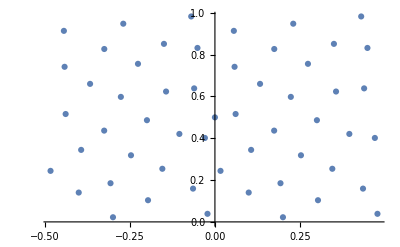

```mathematica
ListPlot[{{0,1/2},{ArcCos[-13/(√(169+2856 Sin[(2 π)/55]^2))]/(2 π),1/110 (55+2 √714 Cos[(2 π)/55])},{ArcCos[29/(√(841+2184 Sin[(4 π)/55]^2))]/(2 π),1/110 (55+2 √546 Cos[(4 π)/55])},{ArcCos[-39/(√(1521+1504 Sin[(6 π)/55]^2))]/(2 π),1/110 (55+4 √94 Cos[(6 π)/55])},{ArcCos[3/(√(9+3016 Sin[(8 π)/55]^2))]/(2 π),1/110 (55+2 √754 Cos[(8 π)/55])},{ArcCos[9/(√(81+40 Sin[(2 π)/11]^2))]/(2 π),1/22 (11+2 √10 Cos[(2 π)/11])},{ArcCos[-23/(√(529+2496 Sin[(12 π)/55]^2))]/(2 π),1/110 (55+8 √39 Cos[(12 π)/55])},{ArcCos[19/(√(361+2664 Cos[(27 π)/110]^2))]/(2 π),1/110 (55+6 √74 Sin[(27 π)/110])},{ArcCos[-49/(√(2401+624 Cos[(23 π)/110]^2))]/(2 π),1/110 (55+4 √39 Sin[(23 π)/110])},{ArcCos[-7/(√(49+2976 Cos[(19 π)/110]^2))]/(2 π),1/110 (55+4 √186 Sin[(19 π)/110])},{ArcCos[7/(√(49+72 Cos[(3 π)/22]^2))]/(2 π),1/22 (11+6 √2 Sin[(3 π)/22])},{ArcCos[-3 √(1/341 (19-2 √5))]/(2 π),1/10 (4+√5)},{ArcCos[9/(√(81+2944 Cos[(7 π)/110]^2))]/(2 π),1/110 (55+8 √46 Sin[(7 π)/110])},{ArcCos[51/(√(2601+424 Cos[(3 π)/110]^2))]/(2 π),1/110 (55+2 √106 Sin[(3 π)/110])},{ArcCos[-17/(√(289+2736 Cos[π/110]^2))]/(2 π),1/110 (55-12 √19 Sin[π/110])},{ArcCos[5/(√(25+96 Cos[π/22]^2))]/(2 π),1/22 (11-4 √6 Sin[π/22])},{ArcCos[-43/(√(1849+1176 Cos[(9 π)/110]^2))]/(2 π),1/110 (55-14 √6 Sin[(9 π)/110])},{ArcCos[-1/(√(1+3024 Cos[(13 π)/110]^2))]/(2 π),1/110 (55-12 √21 Sin[(13 π)/110])},{ArcCos[41/(√(1681+1344 Cos[(17 π)/110]^2))]/(2 π),1/110 (55-8 √21 Sin[(17 π)/110])},{ArcCos[-27/(√(729+2296 Cos[(21 π)/110]^2))]/(2 π),1/110 (55-2 √574 Sin[(21 π)/110])},{ArcCos[3/(√(9+112 Cos[(5 π)/22]^2))]/(2 π),1/22 (11-4 √7 Sin[(5 π)/22])},{ArcCos[-53/(√(2809+216 Sin[(13 π)/55]^2))]/(2 π),1/110 (55-6 √6 Cos[(13 π)/55])},{ArcCos[-√(1/211 (16+3 √5))]/(2 π),1/20 (10-√6-√30)},{ArcCos[31/(√(961+2064 Sin[(9 π)/55]^2))]/(2 π),1/110 (55-4 √129 Cos[(9 π)/55])},{ArcCos[-37/(√(1369+1656 Sin[(7 π)/55]^2))]/(2 π),1/110 (55-6 √46 Cos[(7 π)/55])},{ArcCos[1/(√(1+120 Sin[π/11]^2))]/(2 π),1/22 (11-2 √30 Cos[π/11])},{ArcCos[47/(√(2209+816 Sin[(3 π)/55]^2))]/(2 π),1/110 (55-4 √51 Cos[(3 π)/55])},{ArcCos[-21/(√(441+2584 Sin[π/55]^2))]/(2 π),1/110 (55-2 √646 Cos[π/55])},{-ArcCos[21/(√(441+2584 Sin[π/55]^2))]/(2 π),1/110 (55-2 √646 Cos[π/55])},{-ArcCos[-47/(√(2209+816 Sin[(3 π)/55]^2))]/(2 π),1/110 (55-4 √51 Cos[(3 π)/55])},{-ArcCos[-1/(√(1+120 Sin[π/11]^2))]/(2 π),1/22 (11-2 √30 Cos[π/11])},{-ArcCos[37/(√(1369+1656 Sin[(7 π)/55]^2))]/(2 π),1/110 (55-6 √46 Cos[(7 π)/55])},{-ArcCos[-31/(√(961+2064 Sin[(9 π)/55]^2))]/(2 π),1/110 (55-4 √129 Cos[(9 π)/55])},{-ArcCos[√(1/211 (16+3 √5))]/(2 π),1/20 (10-√6-√30)},{-ArcCos[53/(√(2809+216 Sin[(13 π)/55]^2))]/(2 π),1/110 (55-6 √6 Cos[(13 π)/55])},{-ArcCos[-3/(√(9+112 Cos[(5 π)/22]^2))]/(2 π),1/22 (11-4 √7 Sin[(5 π)/22])},{-ArcCos[27/(√(729+2296 Cos[(21 π)/110]^2))]/(2 π),1/110 (55-2 √574 Sin[(21 π)/110])},{-ArcCos[-41/(√(1681+1344 Cos[(17 π)/110]^2))]/(2 π),1/110 (55-8 √21 Sin[(17 π)/110])},{-ArcCos[1/(√(1+3024 Cos[(13 π)/110]^2))]/(2 π),1/110 (55-12 √21 Sin[(13 π)/110])},{-ArcCos[43/(√(1849+1176 Cos[(9 π)/110]^2))]/(2 π),1/110 (55-14 √6 Sin[(9 π)/110])},{-ArcCos[-5/(√(25+96 Cos[π/22]^2))]/(2 π),1/22 (11-4 √6 Sin[π/22])},{-ArcCos[17/(√(289+2736 Cos[π/110]^2))]/(2 π),1/110 (55-12 √19 Sin[π/110])},{-ArcCos[-51/(√(2601+424 Cos[(3 π)/110]^2))]/(2 π),1/110 (55+2 √106 Sin[(3 π)/110])},{-ArcCos[-9/(√(81+2944 Cos[(7 π)/110]^2))]/(2 π),1/110 (55+8 √46 Sin[(7 π)/110])},{-ArcCos[3 √(1/341 (19-2 √5))]/(2 π),1/10 (4+√5)},{-ArcCos[-7/(√(49+72 Cos[(3 π)/22]^2))]/(2 π),1/22 (11+6 √2 Sin[(3 π)/22])},{-ArcCos[7/(√(49+2976 Cos[(19 π)/110]^2))]/(2 π),1/110 (55+4 √186 Sin[(19 π)/110])},{-ArcCos[49/(√(2401+624 Cos[(23 π)/110]^2))]/(2 π),1/110 (55+4 √39 Sin[(23 π)/110])},{-ArcCos[-19/(√(361+2664 Cos[(27 π)/110]^2))]/(2 π),1/110 (55+6 √74 Sin[(27 π)/110])},{-ArcCos[23/(√(529+2496 Sin[(12 π)/55]^2))]/(2 π),1/110 (55+8 √39 Cos[(12 π)/55])},{-ArcCos[-9/(√(81+40 Sin[(2 π)/11]^2))]/(2 π),1/22 (11+2 √10 Cos[(2 π)/11])},{-ArcCos[-3/(√(9+3016 Sin[(8 π)/55]^2))]/(2 π),1/110 (55+2 √754 Cos[(8 π)/55])},{-ArcCos[39/(√(1521+1504 Sin[(6 π)/55]^2))]/(2 π),1/110 (55+4 √94 Cos[(6 π)/55])},{-ArcCos[-29/(√(841+2184 Sin[(4 π)/55]^2))]/(2 π),1/110 (55+2 √546 Cos[(4 π)/55])},{-ArcCos[13/(√(169+2856 Sin[(2 π)/55]^2))]/(2 π),1/110 (55+2 √714 Cos[(2 π)/55])}}]
```

```mathematica
newlattice[th_]:=Flatten/@({x,y}/.#&/@((RotationMatrix[th,{0,1,0}].#&/@sphFLPS[8])//NSolve[phi[x,y]==#,{x,y}∈Rectangle[{0,0},{.5,1.}]]&/@#&));
```

```mathematica
(*ListPlot[newlattice[Pi/3]]
```

```mathematica
(*ListPlot[newlattice[Pi/4]]
```

```mathematica
(*Manipulate[
ListPlot[newlattice[x]],{x,0,Pi/2}]
```

```mathematica
newcyl[th1_,th2_,th3_,n_]:=psi/@(RotationMatrix[th2,{0,1,0}].RotationMatrix[th3,{1,0,0}].RotationMatrix[th1,{0,0,1}].#&/@sphFLPS[n])
```

```mathematica
(*Manipulate[picture2[newcyl[th1,th2,th3,10]],{th1,-Pi,Pi},{th2,-Pi,Pi},{th3,-Pi,Pi}]
```

```mathematica
(*Manipulate[picture3[newcyl[th1,th2,th3,10],10],{th1,-Pi,Pi},{th2,-Pi,Pi},{th3,-Pi,Pi}]
```

```mathematica
strips[n_]:=Manipulate[picture3[newcyl[th1,th2,th3,n],n,o1,o2],{{th1,0},-Pi,Pi},{{th2,0},-Pi,Pi},{{th3,0+epsilon},-Pi,Pi},{{o1,1},0,1},{o2,0,1}]
```

```mathematica
strips[11]
```

```mathematica
newlin[th1_,th2_,th3_,n_]:={0,0,#}&/@(Part[#,3]&/@newcyl[th1,th2,th3,n])

picture4[X_,n_,o1_,o2_]:=Graphics3D[{
Red,Opacity[o2],Table[Cylinder[{{0,0,-1+i/Fibonacci[n]},{0,0,-1+(i+2)/Fibonacci[n]}},1-epsilon],{i,0,2*Fibonacci[n],4}]
,Opacity[o1],White, Cylinder[{{0,0,-1},{0,0,1}},1-epsilon],
Opacity[1],Black,PointSize[Large],Point@X
}, Boxed->False,ImageSize->Medium,ViewPoint->{0,Infinity,0},ImageSize->Large]

zstrips[n_]:=Manipulate[Graphics3D[{PointSize[.005], Point@newlin[th1,th2,th3,n]},Boxed->False],{{th1,0},-Pi,Pi},{{th2,0},-Pi,Pi},{{th3,0+epsilon},-Pi,Pi}]
```

```mathematica
zstrips[10]
```

```mathematica
zstrips[11]
```

```mathematica
zstrips[15]
```